# Newton' s method for two functions

Define a function. This is the one from the lecture, not the syntax for defining a function

```mathematica
f[x_,y_]:={x + 2 y + 0.05x y -1,-0.1 x +y - 0.01 y -1}
```

(Function calls have square brackets

```mathematica
f[1,1]
```

{2.05,-0.11}

This is the Jacobian matrix, note the extra brackets around the things you differentiate wrt

```mathematica
J=D[f[x,y],{{x,y}}]
```

{{1+0.05 y,2+0.05 x},{-0.1,0.99}}

If you want to make it look like a matrix do this

```mathematica
J//MatrixForm
```

(1+0.05 y | 2+0.05 x
-0.1 | 0.99)

The determinant ... note the xy cancels out

```mathematica
Det[J]
```

1.19+0.005 x+0.0495 y

Start of iteration, curly brackets defien a matrix or vector

```mathematica
X0={1,1}
```

{1,1}

X is going to be the vector of solutions I called x_m in the lecture

```mathematica
X=X0
```

{1,1}

To evaluate the inverse at each point we need to substitute x an y for the components of the vector. This seems a bit messy, it might have been better to define f as a function of a vector .

```mathematica
(Inverse[J]/.x->X[[1]]/.y->X[[2]])
```

{{0.7955,-1.64725},{0.0803536,0.843712}}

This is our iteration step. It overwrites  X each time. No need to work out the inverse each time of course so it would have been better to save the inverse in a variable

```mathematica
X=X - (Inverse[J]/.x->X[[1]]/.y->X[[2]]).f[X[[1]],X[[2]]]
```

{-0.811973,0.928084}

(* You hit shift enter on this each time to get an iteration

```mathematica
f[X[[1]],X[[2]]]
```

{0.00651553,0.}

This is a plot to see where the curves cross. ContourPlot plots one implicitly defined curve while Show combines the two plots

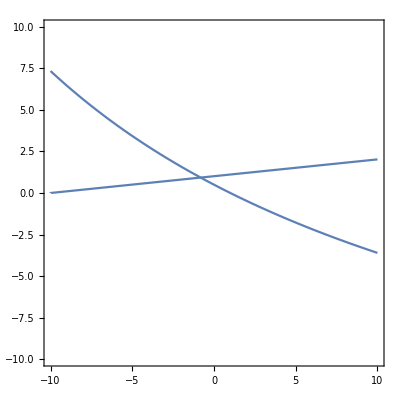

```mathematica
Show[{ContourPlot[x + 2 y + 0.05x y ==1,{x,-10,10},{y,-10,10}],ContourPlot[-0.1 x +y - 0.01 y ==1,{x,-10,10},{y,-10,10}]}]
```